```mathematica
sol=NDSolveValue[{x'[t]==y[t],y'[t]==-20/0.3*x[t],x[0]==1,y[0]==1},{x[t],y[t]},{t,0,10}];
```

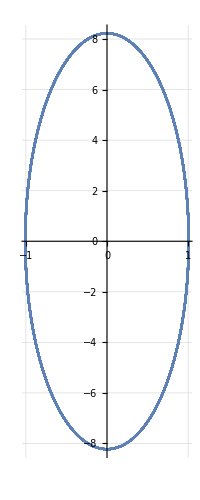

```mathematica
ParametricPlot[sol,{t,0,10},GridLines->Automatic]
```

### C++

```mathematica
eulerExplmy=Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\ODE\\Программа\\ODE\\Эйлер_явный_mx.txt","Table"];
eulerImplmy=Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\ODE\\Программа\\ODE\\Эйлер_неявный_mx.txt","Table"];
```

Явный метод Эйлера:

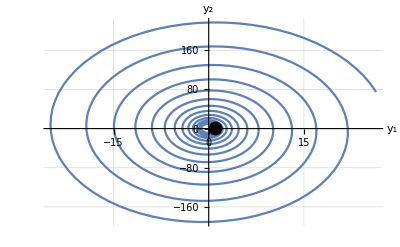

Неявный метод Эйлера:

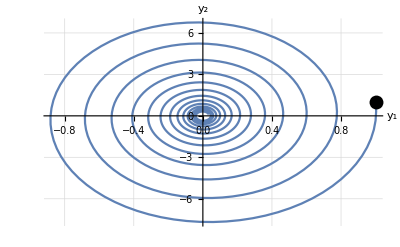

Симметричная схема:

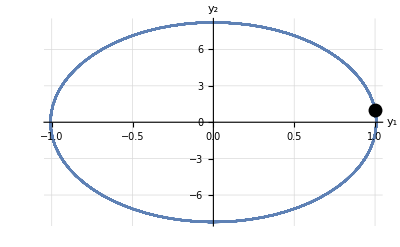

Метод Рунге-Кутты 2 порядка:

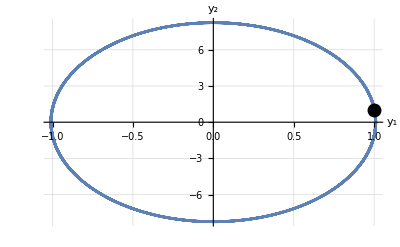

```mathematica
eulerExpl=Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\ODE\\Программа\\ODE\\Маятник_явнЭйлер.txt","Table"];
eulerImpl=Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\ODE\\Программа\\ODE\\Маятник_неявнЭйлер.txt","Table"];
symm=Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\ODE\\Программа\\ODE\\Маятник_симметричная.txt","Table"];
rk2=Import["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\ODE\\Программа\\ODE\\Маятник_РК2.txt","Table"];
Print["Явный метод Эйлера:"];
Show[ListLinePlot[eulerExpl,GridLines->Automatic,AxesLabel->{"y_1","y_2"}],Graphics[{PointSize[0.025],Point@First@eulerExpl}]]
Print["Неявный метод Эйлера:"];
Show[ListLinePlot[eulerImpl,GridLines->Automatic,AxesLabel->{"y_1","y_2"}],Graphics[{PointSize[0.025],Point@First@eulerImpl}]]
Print["Симметричная схема:"];
Show[ListLinePlot[symm,GridLines->Automatic,AxesLabel->{"y_1","y_2"}],Graphics[{PointSize[0.025],Point@First@symm}]]
Print["Метод Рунге-Кутты 2 порядка:"];
Show[ListLinePlot[rk2,GridLines->Automatic,AxesLabel->{"y_1","y_2"}],Graphics[{PointSize[0.025],Point@First@rk2}]]
```

Симметричная схема

```mathematica
G=({{0, 1}, {-ω^2, 0}});
```

```mathematica
Solve[({yn1,yn2}-{y1,y2})/τ==1/2(G.{y1,y2}+G.{yn1,yn2}),{yn1,yn2}]
```

{{yn1→-(-4 y1-4 y2 τ+y1 τ^2 ω^2)/(4+τ^2 ω^2),yn2→-(-4 y2+4 y1 τ ω^2+y2 τ^2 ω^2)/(4+τ^2 ω^2)}}

```mathematica
Inverse@G//MatrixForm
```

(0 | -1/ω^2
1 | 0)

```mathematica
({{0, -1/ω^2}, {1, 0}}).Transpose[G]
```

{{-1/ω^2,0},{0,-ω^2}}

```mathematica
{{-1/ω^2,0},{0,-ω^2}}//MatrixForm
```

(-1/ω^2 | 0
0 | -ω^2)

```mathematica
Eigenvalues@G
```

{-ⅈ ω,ⅈ ω}

```mathematica
{v1,v2}=Eigenvectors@G
```

{{ⅈ/ω,1},{-ⅈ/ω,1}}

```mathematica
v1.v2
```

1+1/ω^2

```mathematica
√(v2.Conjugate@v1)
```

√(1-1/(ω Conjugate[ω]))

```mathematica
√(v1.v1)
```

√(1-1/ω^2)

```mathematica
Simplify[Transpose@{v1,v2}.ConjugateTranspose[Transpose@{v1,v2}],Assumptions->ω∈Reals]//MatrixForm
```

(2/ω^2 | 0
0 | 2)

```mathematica
FullSimplify[((2+ⅈ τ)/(2-ⅈ τ))^n,Assumptions->{τ∈Reals,n∈PositiveIntegers}]
```

(-1+(4 ⅈ)/(2 ⅈ+τ))^n

```mathematica
D[f[1+k x,y],x]/.x->0
```

k f^(1,0)[1,y]